# Unit 1 · Reading a Sequence, Writing a Sequence

## Deep LSTMs as encoder and decoder (Sutskever, Vinyals and Le, 2014) — TensorNets units of learning, 1 of 4

© 2026 Computational Classnotes · CC BY-NC-SA 4.0

A translator can be two recurrent networks: one reads the whole sentence into a fixed-size vector, the other writes the translation from it. This unit builds that machine from plain arrays, one part per section, and checks each part against Wolfram’s own layers. Evaluate the notebook from top to bottom; every section ends with a check that returns True or a number quoted in the write-up “Unit 1 · Reading a Sequence, Writing a Sequence”, which has the same section numbers.

Before you start: choose Evaluation ▸ Quit Kernel ▸ Local, so no definitions from other notebooks interfere. The whole unit evaluates in under a minute.

## 1. Toolkit

Every function the unit uses, in one cell. σ is the logistic function. lstmStep is one step of an LSTM, written from its four gate equations (§3). lstmRun runs it over a sequence, deepRun stacks several LSTMs (§4), decodeStep is one step of the decoder (§5). withStates gives a Wolfram LSTM layer its starting states as inputs. clipNorm, rate and beam are the training and decoding recipes of §7 and §8.

```mathematica
(* id: 30393a5c-3400-4f20-8097-83bbf1c57505 · unit1_seq2seq · cell 1 of 21 · updated 2026-11-24 06:40 UTC *)
σ[x_] := 1/(1 + Exp[-x]);
gates = Flatten@Table[g <> "Gate" <> p, {g, {"Input", "Forget", "Output", "Memory"}}, {p, {"InputWeights", "StateWeights", "Biases"}}];
weightsOf[lstm_] := AssociationMap[Normal@NetExtract[lstm, #] &, gates];      (* the arrays inside a LongShortTermMemoryLayer *)
lstmStep[w_Association][{h_, c_}, x_] := Module[{i, f, o, g, c1},
   i = σ[w["InputGateInputWeights"] . x + w["InputGateStateWeights"] . h + w["InputGateBiases"]];
   f = σ[w["ForgetGateInputWeights"] . x + w["ForgetGateStateWeights"] . h + w["ForgetGateBiases"]];
   o = σ[w["OutputGateInputWeights"] . x + w["OutputGateStateWeights"] . h + w["OutputGateBiases"]];
   g = Tanh[w["MemoryGateInputWeights"] . x + w["MemoryGateStateWeights"] . h + w["MemoryGateBiases"]];
   c1 = f c + i g;
   {o Tanh[c1], c1}];
lstmRun[w_Association, xs_List, init_List] := Rest@FoldList[lstmStep[w], init, xs];   (* the list of {h, c} after each step *)
zeroState[n_Integer] := {ConstantArray[0., n], ConstantArray[0., n]};
deepRun[ws_List, xs_List] := Module[{seq = xs, finals = {}, run},
   Do[run = lstmRun[w, seq, zeroState[Length[w["InputGateBiases"]]]]; seq = run[[All, 1]]; AppendTo[finals, Last[run]], {w, ws}];
   <|"Outputs" -> seq, "FinalStates" -> finals|>];
decodeStep[ws_List, wOut_, bOut_][states_List, x0_] := Module[{x = x0, new = {}, st},
   Do[st = lstmStep[ws[[k]]][states[[k]], x]; AppendTo[new, st]; x = st[[1]], {k, Length[ws]}];
   <|"Probabilities" -> Exp[#]/Total[Exp[#]] &[wOut . x + bOut], "States" -> new|>];
withStates[lstm_] := NetGraph[{lstm}, {NetPort["Input"] -> 1, NetPort["h0"] -> NetPort[1, "State"],
    NetPort["c0"] -> NetPort[1, "CellState"], NetPort[1, "Output"] -> NetPort["Output"], NetPort[1, "CellState"] -> NetPort["CFinal"]}];
uniformInit[net_NetChain] := Module[{n, u = UniformDistribution[{-0.08, 0.08}]},
   n = NetInitialize[net, All, Method -> {"Random", "Weights" -> u, "Biases" -> u}];
   Fold[NetReplacePart[#1, {#2, "ForgetGateBiases"} -> RandomVariate[u, Length@Normal@NetExtract[#1, {#2, "ForgetGateBiases"}]]] &,
    n, Flatten@Position[Normal[n], _LongShortTermMemoryLayer, {1}, Heads -> False]]];
clipNorm[g_List, s_ : 5] := With[{n = Norm[Flatten[g]]}, If[n > s, g s/n, g]];
cosine[a_, b_] := Flatten[a] . Flatten[b]/(Norm[Flatten[a]] Norm[Flatten[b]]);
rate[epoch_?NumericQ] := If[epoch < 5, 0.7, 0.7*0.5^(Floor[(epoch - 5)/0.5] + 1)];
beam[logP_, start_, eos_, width_Integer, maxLen_Integer] := Module[{beams = {{{start}, 0.}}, done = {}, cands},
   Do[cands = Flatten[Table[KeyValueMap[{Append[b[[1]], #1], b[[2]] + #2} &, logP[b[[1]]]], {b, beams}], 1];
    cands = TakeLargestBy[cands, Last, UpTo[width]];
    done = Join[done, Select[cands, Last[First[#]] === eos &]];
    beams = Select[cands, Last[First[#]] =!= eos &];
    If[beams === {}, Break[]], {maxLen}];
   SortBy[If[done === {}, beams, done], -Last[#] &]];
lstmParams[nIn_Integer, n_Integer] := 4 (n nIn + n n + n);
SeedRandom[2014];
```

## 2. The idea: read everything, then write

A sentence and its translation rarely have the same length, and word i of one is not word i of the other. So the paper uses two networks. The encoder reads the source one word at a time and ends in a fixed-size vector v, the “thought vector”. The decoder starts from v and writes the target one word at a time, feeding each word it writes back in as its next input, until it writes <EOS>.

p(y₁, …, y_T′ | x₁, …, x_T) = ∏ₜ p(yₜ | v, y₁, …, yₜ₋₁)

Three choices made it work (Section 2 of the paper): two different LSTMs for reading and writing, four layers deep, and the source fed in reverse (§6).

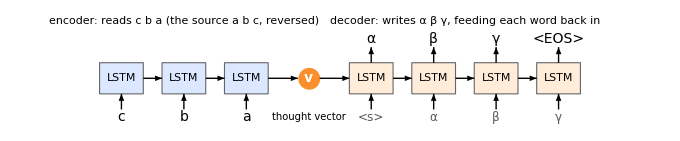

```mathematica
(* id: 6dd42ca9-78d6-42b9-9ea5-1869f26f93f3 · unit1_seq2seq · cell 2 of 21 · updated 2026-11-24 06:40 UTC *)
box[x_, lab_, col_] := {EdgeForm[GrayLevel[0.4]], col, Rectangle[{x, 0}, {x + 1.4, 1}], Black, Text[Style[lab, 11], {x + 0.7, 0.5}]};
Graphics[{Arrowheads[0.018],
  Table[{box[2 i, "LSTM", RGBColor[0.86, 0.91, 1]], Text[Style[{"c", "b", "a"}[[i + 1]], 14, Italic], {2 i + 0.7, -0.75}],
     Arrow[{{2 i + 0.7, -0.5}, {2 i + 0.7, 0}}]}, {i, 0, 2}],
  Table[Arrow[{{2 i + 1.4, 0.5}, {2 i + 2, 0.5}}], {i, 0, 1}], Arrow[{{5.4, 0.5}, {6.35, 0.5}}],
  {RGBColor[0.98, 0.56, 0.17], Disk[{6.7, 0.5}, 0.35]}, Text[Style["v", Bold, 14, White], {6.7, 0.5}], Arrow[{{7.05, 0.5}, {8, 0.5}}],
  Table[{box[8 + 2 i, "LSTM", RGBColor[1, 0.93, 0.85]], Text[Style[{"α", "β", "γ", "<EOS>"}[[i + 1]], 14, Italic], {8.7 + 2 i, 1.75}],
     Arrow[{{8.7 + 2 i, 1}, {8.7 + 2 i, 1.5}}], Text[Style[{"<s>", "α", "β", "γ"}[[i + 1]], 12, Italic, GrayLevel[0.35]], {8.7 + 2 i, -0.75}],
     Arrow[{{8.7 + 2 i, -0.5}, {8.7 + 2 i, 0}}]}, {i, 0, 3}],
  Table[Arrow[{{9.4 + 2 i, 0.5}, {10 + 2 i, 0.5}}], {i, 0, 2}],
  Text[Style["encoder: reads c b a (the source a b c, reversed)", 11], {2.7, 2.35}],
  Text[Style["decoder: writes α β γ, feeding each word back in", 11], {11.7, 2.35}],
  Text[Style["thought vector", 10], {6.7, -0.75}]}, ImageSize -> 680, PlotRange -> {{-1.2, 16.6}, {-1.1, 2.6}}]
```

Fig. 1. The encoder–decoder. The encoder reads the reversed source and ends in the thought vector v; the decoder starts from v and writes the target, one word per step, reading back the word it has just written.

## 3. The LSTM cell

An LSTM keeps two vectors: the hidden state h, which it shows to the next layer, and the memory cell c, which it keeps for itself. At each step it reads an input x and computes four gates from x and the previous h. Each gate is a number between 0 and 1 per cell, except g, the new content, which is between −1 and 1.

i = σ(W_i x + U_i h + b_i)    f = σ(W_f x + U_f h + b_f)    o = σ(W_o x + U_o h + b_o)    g = tanh(W_g x + U_g h + b_g)

c′ = f c + i g        h′ = o tanh(c′)

i decides how much new content to write, f how much old memory to keep, o how much of the memory to show. The memory is updated by addition, not by repeated multiplication with a weight matrix, which is what lets information and gradients survive over long sentences.

### 3.1 Worked by hand: one step of a one-cell LSTM

Take one input and one cell, every weight 0.5 and every bias 0, start from h = c = 0 and read x = 1. Every gate sees 0.5 · 1 + 0.5 · 0 + 0 = 0.5. So i = f = o = σ(0.5) = 1/(1 + e^−0.5) = 0.6225, and g = tanh(0.5) = 0.4621. The memory becomes c′ = 0.6225 · 0 + 0.6225 · 0.4621 = 0.2877. The output is h′ = 0.6225 · tanh(0.2877) = 0.6225 · 0.2800 = 0.1743.

```mathematica
(* id: 096f9a14-c123-4235-9938-dda52ab1d0c0 · unit1_seq2seq · cell 3 of 21 · updated 2026-11-24 06:40 UTC *)
w1 = AssociationMap[If[StringEndsQ[#, "Biases"], {0.}, {{0.5}}] &, gates];
lstmStep[w1][{{0.}, {0.}}, {1.}]
```

{{0.17427},{0.287649}}

Check: {{0.1743}, {0.2877}}, the h′ and c′ computed by hand.

### 3.2 The same cell as Wolfram’s layer

LongShortTermMemoryLayer stores exactly these twelve arrays: InputGate…, ForgetGate…, OutputGate… and MemoryGate… (Wolfram calls g the memory gate). Copy them out of a random layer and run our lstmStep over a sequence; the hidden states must agree.

```mathematica
(* id: f3ef1c87-e68c-401f-8eb6-e2969f9d828f · unit1_seq2seq · cell 4 of 21 · updated 2026-11-24 06:40 UTC *)
layer = NetInitialize@LongShortTermMemoryLayer[6, "Input" -> {"Varying", 4}];
xs = RandomReal[{-1, 1}, {7, 4}];
Max@Abs[lstmRun[weightsOf[layer], xs, zeroState[6]][[All, 1]] - layer[xs]] < 10^-5
```

True

Check: True (7 steps, 4 inputs, 6 cells). The layer can also start from given states, as the decoder must; its ports State and CellState are h and c, reached through NetGraph (withStates in §1):

```mathematica
(* id: 2c31d887-d4f1-40fb-88eb-e8e1208a9b1f · unit1_seq2seq · cell 5 of 21 · updated 2026-11-24 06:40 UTC *)
h0 = RandomReal[{-1, 1}, 6]; c0 = RandomReal[{-1, 1}, 6];
out = withStates[layer][<|"Input" -> xs, "h0" -> h0, "c0" -> c0|>];
Max@Abs[lstmRun[weightsOf[layer], xs, {h0, c0}][[All, 1]] - out["Output"]] < 10^-5 &&
 Max@Abs[Last[lstmRun[weightsOf[layer], xs, {h0, c0}]][[2]] - out["CFinal"]] < 10^-5
```

True

Check: True.

### 3.3 The forget gate sets how long memory lasts

A one-cell LSTM reads a single pulse, x = 1 at step 1 and 0 afterwards. Only the forget-gate bias changes between the three curves. With f = σ(3) = 0.95 the memory fades slowly; with f = σ(−3) = 0.05 it is gone after two steps.

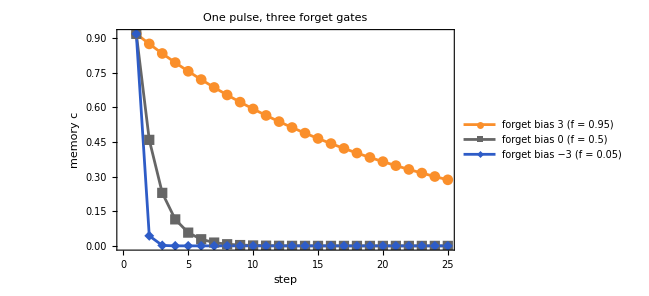

```mathematica
(* id: ba025d43-5797-405b-b727-a098801b90e4 · unit1_seq2seq · cell 6 of 21 · updated 2026-11-24 06:40 UTC *)
pulseCell[bf_] := <|"InputGateInputWeights" -> {{5.}}, "InputGateStateWeights" -> {{0.}}, "InputGateBiases" -> {-2.},
   "ForgetGateInputWeights" -> {{0.}}, "ForgetGateStateWeights" -> {{0.}}, "ForgetGateBiases" -> {bf},
   "OutputGateInputWeights" -> {{0.}}, "OutputGateStateWeights" -> {{0.}}, "OutputGateBiases" -> {5.},
   "MemoryGateInputWeights" -> {{2.}}, "MemoryGateStateWeights" -> {{0.}}, "MemoryGateBiases" -> {0.}|>;
pulse = Prepend[ConstantArray[{0.}, 24], {1.}];
ListLinePlot[Table[lstmRun[pulseCell[bf], pulse, zeroState[1]][[All, 2, 1]], {bf, {3., 0., -3.}}],
 PlotLegends -> {"forget bias 3 (f = 0.95)", "forget bias 0 (f = 0.5)", "forget bias −3 (f = 0.05)"},
 PlotStyle -> {RGBColor[0.98, 0.56, 0.17], GrayLevel[0.4], RGBColor[0.18, 0.36, 0.78]}, PlotMarkers -> Automatic,
 Frame -> True, FrameLabel -> {"step", "memory c"}, PlotLabel -> "One pulse, three forget gates", ImageSize -> 480,
 ImagePadding -> {{50, 10}, {40, 30}}]
```

Fig. 2. The memory c of a one-cell LSTM after one input pulse. After the pulse c is multiplied by f at every step, so it decays like fᵗ.

```mathematica
(* id: 67878510-ea4f-48e4-afdf-8b358b19d844 · unit1_seq2seq · cell 7 of 21 · updated 2026-11-24 06:40 UTC *)
With[{c = lstmRun[pulseCell[3.], pulse, zeroState[1]][[All, 2, 1]]}, Abs[c[[3]]/c[[2]] - σ[3.]] < 10^-12]
```

True

Check: True. After the pulse the ratio of successive memories is exactly f = σ(3) = 0.9526.

## 4. A deep encoder and its thought vector

The paper stacks four LSTMs. Layer k reads the hidden states of layer k − 1, so higher layers see a more processed sentence. After the last source word, the final (h, c) of every layer is kept: that is the thought vector, 2 × 4 × 1000 = 8000 numbers in the paper’s model.

```mathematica
(* id: f2068ac8-8223-48e7-8831-5abb0cf3054b · unit1_seq2seq · cell 8 of 21 · updated 2026-11-24 06:40 UTC *)
chain = NetInitialize@NetChain[{LongShortTermMemoryLayer[5], LongShortTermMemoryLayer[5], LongShortTermMemoryLayer[5]}, "Input" -> {"Varying", 3}];
src = RandomReal[{-1, 1}, {6, 3}];
enc = deepRun[weightsOf /@ Table[NetExtract[chain, k], {k, 3}], src];
{Max@Abs[enc["Outputs"] - chain[src]] < 10^-5, Length@Flatten[enc["FinalStates"]], 2*4*1000}
```

{True,30,8000}

Check: {True, 30, 8000}. Our three-layer stack equals NetChain of three LongShortTermMemoryLayers; its thought vector has 2 × 3 × 5 = 30 numbers; the paper’s has 8000.

## 5. The decoder

The decoder is a second deep LSTM with its own weights. Its layers start from the encoder’s final states. At each step it reads the embedding of the previous word, and a softmax over the target vocabulary turns its top hidden state into probabilities for the next word.

p(next word = k) = exp(z_k) / Σⱼ exp(z_j),    z = W h + b

### 5.1 Worked by hand: a softmax

For scores z = (2, 1, 0): e.b2 = 7.389, e.b9 = 2.718, e⁰ = 1, total 11.107. The probabilities are 7.389/11.107 = 0.665, 2.718/11.107 = 0.245 and 1/11.107 = 0.090. They are positive and sum to 1; adding the same number to every score changes nothing.

```mathematica
(* id: e104ab66-f262-4261-b6d7-4c33545d149f · unit1_seq2seq · cell 9 of 21 · updated 2026-11-24 06:40 UTC *)
{Exp[#]/Total[Exp[#]] &[{2., 1., 0.}], Exp[#]/Total[Exp[#]] &[{2., 1., 0.} + 10]}
```

{{0.665241,0.244728,0.0900306},{0.665241,0.244728,0.0900306}}

Check: {0.665, 0.245, 0.090} twice.

### 5.2 One decoder step, started from the thought vector

```mathematica
(* id: 2d3d8292-9b3a-4400-bd1f-22f1da203f46 · unit1_seq2seq · cell 10 of 21 · updated 2026-11-24 06:40 UTC *)
encNet = NetInitialize@NetChain[{LongShortTermMemoryLayer[4], LongShortTermMemoryLayer[4]}, "Input" -> {"Varying", 3}];
decNet = NetInitialize@NetChain[{LongShortTermMemoryLayer[4], LongShortTermMemoryLayer[4]}, "Input" -> {"Varying", 3}];
thought = deepRun[weightsOf /@ {NetExtract[encNet, 1], NetExtract[encNet, 2]}, RandomReal[{-1, 1}, {5, 3}]]["FinalStates"];
emb = RandomReal[{-1, 1}, 3];
step = decodeStep[weightsOf /@ {NetExtract[decNet, 1], NetExtract[decNet, 2]}, RandomReal[{-0.5, 0.5}, {10, 4}], RandomReal[{-0.1, 0.1}, 10]][thought, emb];
{Min[step["Probabilities"]] > 0, Abs[Total[step["Probabilities"]] - 1] < 10^-12,
 Max@Abs[step["States"][[1, 1]] - withStates[NetExtract[decNet, 1]][<|"Input" -> {emb}, "h0" -> thought[[1, 1]], "c0" -> thought[[1, 2]]|>]["Output"][[1]]] < 10^-5}
```

{True,True,True}

Check: {True, True, True}. The next-word distribution over 10 words is a probability distribution, and the decoder’s first layer, started from the encoder’s states, agrees with Wolfram’s layer.

During training the decoder reads the correct previous word, not its own guess (teacher forcing). At test time it reads its own output, and beam search (§8) chooses which outputs to keep.

## 6. Reversing the source

Feed the source reversed: c, b, a instead of a, b, c, while the target stays α, β, γ. Nothing else changes, yet the paper’s test BLEU rose from 25.9 to 30.6 (Section 3.3). The reason is distance. Put the source at positions 1…T and the target after it at T + 1…2T, with word i of the target aligned to word i of the source.

### 6.1 Worked by hand: T = 3

Forward: a, b, c sit at 1, 2, 3 and α, β, γ at 4, 5, 6. Each pair is 3 apart: 4 − 1 = 5 − 2 = 6 − 3 = 3. Reversed: c, b, a sit at 1, 2, 3, so a is at 3, b at 2, c at 1. The gaps are 4 − 3 = 1, 5 − 2 = 3, 6 − 1 = 5. The average is 3 both ways, but the first pair is now only 1 step apart, so the network can link a to α at once and build from there.

```mathematica
(* id: a2986df3-aefd-45a5-8181-3ab8d0e1cab7 · unit1_seq2seq · cell 11 of 21 · updated 2026-11-24 06:40 UTC *)
lags[T_Integer, reversed_ : False] := Table[(T + i) - If[reversed, T + 1 - i, i], {i, T}];
{lags[3], lags[3, True]}
```

{{3,3,3},{1,3,5}}

Check: {{3, 3, 3}, {1, 3, 5}}.

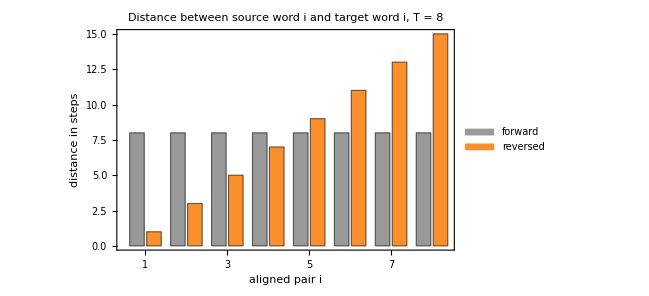

```mathematica
(* id: 89272d08-3199-4c6b-99e1-b02900c49351 · unit1_seq2seq · cell 12 of 21 · updated 2026-11-24 06:40 UTC *)
BarChart[Transpose[{lags[8], lags[8, True]}], ChartStyle -> {GrayLevel[0.6], RGBColor[0.98, 0.56, 0.17]},
 ChartLegends -> {"forward", "reversed"}, ChartLabels -> {Range[8], None}, Frame -> True, FrameLabel -> {"aligned pair i", "distance in steps"},
 PlotLabel -> "Distance between source word i and target word i, T = 8", ImageSize -> 480, ImagePadding -> {{50, 10}, {40, 30}}]
```

Fig. 3. Forward, every aligned pair is T = 8 steps apart. Reversed, the distances are 1, 3, 5, …, 15: the same average, 8, but the first words are neighbours.

```mathematica
(* id: 662c3e89-aadf-4aee-9935-1d8bffd18f10 · unit1_seq2seq · cell 13 of 21 · updated 2026-11-24 06:40 UTC *)
{Mean[lags[8]], Mean[lags[8, True]], Min[lags[8]], Min[lags[8, True]]}
```

{8,8,8,1}

Check: {8, 8, 8, 1}.

## 7. The training recipe

### 7.1 Starting weights, and a Wolfram detail

All parameters start uniformly distributed in [−0.08, 0.08] (Section 3.4). NetInitialize does this with one option, except that it always sets the LSTM forget-gate biases to 1, a later practice recommended by Jozefowicz, Zaremba and Sutskever (2015). To follow the paper, uniformInit (§1) resets those biases too.

```mathematica
(* id: 17034447-9340-4b00-b712-9d8d5801c751 · unit1_seq2seq · cell 14 of 21 · updated 2026-11-24 06:40 UTC *)
plain = NetInitialize[NetChain[{LongShortTermMemoryLayer[20]}, "Input" -> {"Varying", 10}], All,
   Method -> {"Random", "Weights" -> UniformDistribution[{-0.08, 0.08}], "Biases" -> UniformDistribution[{-0.08, 0.08}]}];
paper = uniformInit[NetChain[{LongShortTermMemoryLayer[20], LongShortTermMemoryLayer[20]}, "Input" -> {"Varying", 10}]];
{Union@Flatten@Normal@NetExtract[plain, {1, "ForgetGateBiases"}], Max@Abs@Flatten@Table[Normal@NetExtract[paper, {k, a}], {k, 2}, {a, gates}] <= 0.08}
```

{{1.},True}

Check: {{1.}, True}. Plain NetInitialize leaves every forget-gate bias at 1; after uniformInit every parameter of the two-layer LSTM is within ±0.08.

### 7.2 Clipping the gradient by its norm

LSTMs rarely suffer from vanishing gradients but can suffer from exploding ones. For each batch the paper computes the norm s of the whole gradient g, all parameters together, and if s > 5 rescales g to 5g/s.

s = ‖g‖₂ ;   if s > 5 :  g ← 5 g / s

Let g = (6, 8). Its norm is √(36 + 64) = 10 > 5, so g becomes (6, 8) · 5/10 = (3, 4), whose norm is 5. The direction is unchanged. Clamping each component to ±5 instead would give (5, 5), which points somewhere else.

```mathematica
(* id: 6902c11a-187c-47ac-9d65-b32b8ec9b245 · unit1_seq2seq · cell 15 of 21 · updated 2026-11-24 06:40 UTC *)
{clipNorm[{6., 8.}], clipNorm[{0.3, 0.4}], cosine[{6., 8.}, clipNorm[{6., 8.}]], cosine[{6., 8.}, Clip[{6., 8.}, {-5, 5}]]}
```

{{3.,4.},{0.3,0.4},1.,0.989949}

Check: {{3., 4.}, {0.3, 0.4}, 1., 0.990}. A small gradient is left alone; clipping by the norm keeps the direction (cosine 1), clamping components does not (0.990).

### 7.3 The learning-rate schedule

Plain stochastic gradient descent without momentum, batches of 128 sentences, learning rate 0.7. After 5 epochs the rate is halved every half epoch, and training stops after 7.5 epochs.

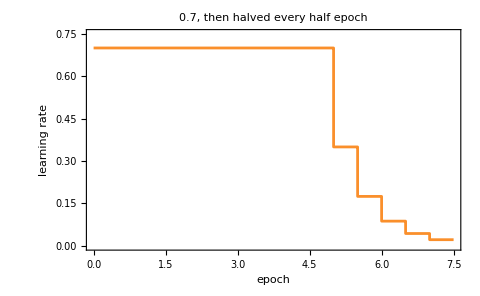

```mathematica
(* id: f83d6684-dd01-4b91-8247-3a6ba501b38d · unit1_seq2seq · cell 16 of 21 · updated 2026-11-24 06:40 UTC *)
Plot[rate[e], {e, 0, 7.5}, Exclusions -> None, PlotRange -> {0, 0.75}, PlotPoints -> 400, PlotStyle -> RGBColor[0.98, 0.56, 0.17],
 Frame -> True, FrameLabel -> {"epoch", "learning rate"}, PlotLabel -> "0.7, then halved every half epoch", ImageSize -> 480,
 ImagePadding -> {{50, 10}, {40, 30}}]
```

Fig. 4. The learning rate over the 7.5 epochs of training.

```mathematica
(* id: e08396da-57c3-4163-baf1-50d3e57797fa · unit1_seq2seq · cell 17 of 21 · updated 2026-11-24 06:40 UTC *)
{rate[4.99], rate[5], rate[5.5], rate[7.4]}
```

{0.7,0.35,0.175,0.021875}

Check: {0.7, 0.35, 0.175, 0.021875}; the last half epoch runs at 0.7/32.

## 8. Beam search

To write, the decoder must choose words. Greedy decoding takes the most likely word at each step. Beam search keeps the B most likely partial outputs instead: each is extended by every word, and the B best of all the extensions are kept. A hypothesis that ends in <EOS> leaves the beam and joins the finished list. The paper finds that B = 1 already works well and that B = 2 gives most of the benefit (Section 3.2).

### 8.1 Worked by hand: a model where greedy goes wrong

A toy model writes A (0.6) or B (0.4) first. After A it hesitates: A 0.3, B 0.3, <e> 0.4. After B it almost always stops: <e> 0.95. Greedy takes A (0.6), then <e> (0.4): the output “A” has probability 0.6 × 0.4 = 0.24. A beam of width 2 keeps both A and B after step 1. At step 2 the six extensions have probabilities A<e> 0.24, AA 0.18, AB 0.18, B<e> 0.38, BA 0.01, BB 0.01. The best two, B<e> and A<e>, are both finished, and B<e> wins with 0.38.

```mathematica
(* id: eca20ce8-8002-4b5a-95e1-906f54ce835e · unit1_seq2seq · cell 18 of 21 · updated 2026-11-24 06:40 UTC *)
toy[prefix_List] := Log /@ Switch[Last[prefix], "<s>", <|"A" -> 0.6, "B" -> 0.4|>,
    "A", <|"A" -> 0.3, "B" -> 0.3, "<e>" -> 0.4|>, "B", <|"A" -> 0.025, "B" -> 0.025, "<e>" -> 0.95|>];
{First@#[[1]], Exp@#[[1, 2]]} & /@ {beam[toy, "<s>", "<e>", 1, 6], beam[toy, "<s>", "<e>", 2, 6]}
```

{{{<s>,A,<e>},0.24},{{<s>,B,<e>},0.38}}

Check: greedy gives {<s>, A, <e>} with probability 0.24; the beam of width 2 gives {<s>, B, <e>} with 0.38.

```mathematica
(* id: 9b709312-1be1-488f-b527-b6dab83787ed · unit1_seq2seq · cell 19 of 21 · updated 2026-11-24 06:40 UTC *)
Graph[{"<s>" -> "A", "<s>" -> "B", "A" -> "A<e>", "A" -> "AA", "A" -> "AB", "B" -> "B<e>", "B" -> "BA", "B" -> "BB"},
 EdgeLabels -> {("<s>" -> "A") -> 0.6, ("<s>" -> "B") -> 0.4, ("A" -> "A<e>") -> 0.4, ("A" -> "AA") -> 0.3, ("A" -> "AB") -> 0.3,
   ("B" -> "B<e>") -> 0.95, ("B" -> "BA") -> 0.025, ("B" -> "BB") -> 0.025},
 VertexLabels -> Placed["Name", Above], GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left},
 EdgeStyle -> {("<s>" -> "B") -> Directive[Thick, RGBColor[0.98, 0.56, 0.17]], ("B" -> "B<e>") -> Directive[Thick, RGBColor[0.98, 0.56, 0.17]],
   ("<s>" -> "A") -> Dashed, ("A" -> "A<e>") -> Dashed},
 VertexSize -> 0.12, AspectRatio -> 0.55, PlotLabel -> "Greedy (dashed) ends with probability 0.24; beam 2 (orange) finds 0.38", ImageSize -> 560,
 ImagePadding -> {{20, 20}, {20, 34}}]
```

-Graphics-

Fig. 5. The search tree of the toy model, with each step’s probability on its edge. Greedy follows the dashed path; the beam of width 2 also keeps B and finds the better output.

## 9. How big is the paper’s model?

An LSTM layer with nᵢₙ inputs and n cells has four gates, each with an n × nᵢₙ input matrix, an n × n state matrix and n biases: 4(n nᵢₙ + n.b2 + n) parameters.

One layer of 1000 cells reading 1000 numbers: 4 × (1 000 000 + 1 000 000 + 1000) = 8 004 000. Eight such layers (4 encoder, 4 decoder) make 64 032 000. The embeddings add 160 000 × 1000 (source) and 80 000 × 1000 (target), 240 000 000 in all. The softmax adds 80 000 × 1000 + 80 000 = 80 080 000. Total: 240 000 000 + 64 032 000 + 80 080 000 = 384 112 000, the paper’s “384M parameters”. Most of them are in the vocabulary, not in the LSTMs.

```mathematica
(* id: 273be9a8-ede7-4f3b-bfb8-02f44b1bfe0d · unit1_seq2seq · cell 20 of 21 · updated 2026-11-24 06:40 UTC *)
{lstmParams[4, 6] == Information[NetInitialize@LongShortTermMemoryLayer[6, "Input" -> {"Varying", 4}], "ArraysTotalElementCount"],
 160000*1000 + 80000*1000 + 8 lstmParams[1000, 1000] + 80000*1000 + 80000}
```

{True,384112000}

Check: {True, 384112000}. The formula agrees with Wolfram’s own count for a small layer, and the total is the paper’s.

## 10. Exercises

1. Repeat the hand computation of §3.1 with x = −1. Which gates change, and why does h′ come out negative?

2. For a source of length T = 10, list the forward and reversed distances of §6 and their averages.

3. What is the learning rate at epoch 6.2?

4. How many parameters has a two-layer LSTM with 256 inputs and 512 cells per layer? Check your answer against Wolfram’s count.

5. In the toy model of §8, change the probability of <e> after A from 0.4 to 0.7. Does greedy decoding still lose?

Answers, computed:

```mathematica
(* id: a9e97f1f-6f89-446a-a02b-ae47a345015b · unit1_seq2seq · cell 21 of 21 · updated 2026-11-24 06:40 UTC *)
{lstmStep[w1][{{0.}, {0.}}, {-1.}],
 {lags[10], lags[10, True], Mean[lags[10]], Mean[lags[10, True]]},
 rate[6.2],
 {lstmParams[256, 512] + lstmParams[512, 512],
  Information[NetInitialize@NetChain[{LongShortTermMemoryLayer[512], LongShortTermMemoryLayer[512]}, "Input" -> {"Varying", 256}], "ArraysTotalElementCount"]},
 With[{toy2 = Function[p, Log /@ Switch[Last[p], "<s>", <|"A" -> 0.6, "B" -> 0.4|>, "A", <|"A" -> 0.15, "B" -> 0.15, "<e>" -> 0.7|>,
       "B", <|"A" -> 0.025, "B" -> 0.025, "<e>" -> 0.95|>]]},
  {First@#[[1]], Exp@#[[1, 2]]} & /@ {beam[toy2, "<s>", "<e>", 1, 6], beam[toy2, "<s>", "<e>", 2, 6]}]}
```

{{{-0.0652085},{-0.174468}},{{10,10,10,10,10,10,10,10,10,10},{1,3,5,7,9,11,13,15,17,19},10,10},0.0875,{3674112,3674112},{{{<s>,A,<e>},0.42},{{<s>,A,<e>},0.42}}}

1: every gate sees −0.5, so i = f = o = σ(−0.5) = 0.3775 and g = tanh(−0.5) = −0.4621; the new content is negative, so c′ and h′ are negative. 4: 3 674 112 both ways. 5: no; greedy now finds A<e> with 0.6 × 0.7 = 0.42, which beats B<e> with 0.38.

## 11. Summary

Two deep LSTMs translate: one reads the whole source into the final states of its layers, the other writes from them, one word at a time. The LSTM’s additive memory, controlled by its forget gate, carries information across the sentence. Reversing the source puts the first words next to each other. Small starting weights, clipping the gradient by its norm and a halving learning rate make training reliable, and a narrow beam finds better outputs than greedy decoding.

Next: Unit 2 turns mathematics into sequences that such a machine can learn from, and Unit 3 replaces the LSTM with attention.

© 2026 Computational Classnotes · CC BY-NC-SA 4.0